```mathematica
Clear[v]
```

```mathematica
EmbedGraph5In6[key5_,key6_]:=Block[{val=allGraphs5[key5], sets, reference={1,2,3,4,5}, g, sub},
sets=val["vertexsets"];
g=allGraphs6[key6,"graph"];
g=EdgeDelete[ g,{1<->2,2<->3,3<->4,4<->5,5<->1}];
(* first contractth edges *)
Table[If[Length[s]>1,
g=VertexContract[g,s]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{First[sets[[e[[1]]]]]<->First[sets[[e[[2]]]]]}],{e,EdgeList[sub]}
];
Graph[VertexList[g],EdgeList[g],VertexLabels->"Name"]
]
```

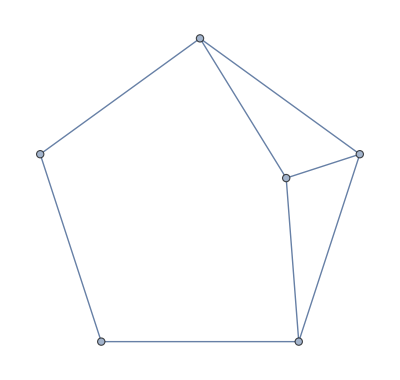

```mathematica
patter= Graph[EdgeAdd[VertexAdd[CycleGraph[5],6],{1<->6,2<->6,3<->6}],GraphLayout->"TutteEmbedding"]
```

```mathematica
Select[Keys[allGraphs6],IsomorphicGraphQ[allGraphs6[#,"graph"],patter]&]
```

{6935062,6935014,6930850,6930688,6929398,6929182,6917752,6917518,6916348,6916108,6911194,6909796,6580930,6580768,6576556,6576348,6574944,6574890,6563298,6563226,6561112,6557682,6557602,6555504,6462838,6462622,6458304,6458250,6457006,6456846,6443748,6443724,6443020,6439536,6439510,6438810,6386080,6384676,6383974,6380464,6379762,6378358,5518072,5517838,5513538,5513466,5511280,5500576,5500416,5498964,5498958,5494752,5494744,5492646,5400028,5399788,5393988,5393964,5393236,5382324,5382318,5381074,5380866,5376702,5376700,5376000,5336392,5334940,5334214,5317678,5316952,5315500,5041362,5041282,5039856,5039830,5039104,5028192,5028184,5026782,5026780,5026078,5022408,5022360,4986634,4980810,4980082,4967760,4967032,4961208,4868596,4864224,4862038,4851126,4848940,4844568,2330128,2325594,2323576,2323416,2323336,2312424,2310526,2310318,2310310,2306154,2306106,2306100,2213488,2207448,2206930,2206722,2206696,2194374,2193832,2193672,2193670,2188062,2188056,2188008,2148448,2148400,2148376,2135350,2135326,2135278,1859034,1857528,1856848,1856800,1856776,1840240,1839540,1839538,1839378,1838142,1838134,1837926,1798690,1798482,1798456,1781220,1781194,1780986,1682056,1681896,1681816,1663182,1663102,1662942,796104,794694,793990,793966,793918,790480,789780,789754,789546,788382,788302,788142,735832,735672,735670,731460,731458,731298,619246,619038,619030,613422,613414,613206,264954,264906,264900,263502,263496,263448}

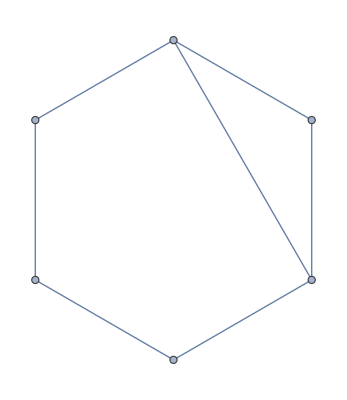

```mathematica
patter2= Graph[EdgeAdd[VertexAdd[CycleGraph[5],6],{1<->6,2<->6}],GraphLayout->"TutteEmbedding"]
```

```mathematica
Select[Keys[allGraphs6],EdgeList[allGraphs6[#,"graph"]]==EdgeList[patter2]&]
```

{5039829}

```mathematica
Map[ShowGraph[allGraphs6,#]&,{5039856,5039850,5039848}]
```

{-Graphics-5039856,-Graphics-5039850,-Graphics-5039848}

```mathematica
ShowGraph[allGraphs6,5039829]
```

-Graphics-5039829

```mathematica
ShowGraph[allGraphs6,5039856]
```

-Graphics-5039856

```mathematica
allGraphs5[alfa1Key,"vertexsets"]
```

{{1,3},{2,4},{5}}

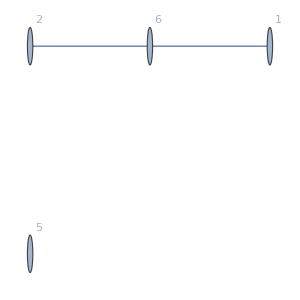

{5,6,1,2}

{1<->6,2<->6,1<->2,5<->1,2<->5}

```mathematica
Graph[EdgeList[EmbedGraph5In6[alfa1Key,5039856]]]
```

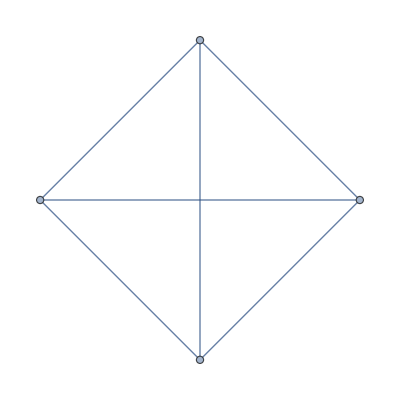

```mathematica
Graph[EdgeList[EmbedGraph5In6[beta1Key,5039856]]]
```

```mathematica
With[{e=Map[Sort[EdgeList[EmbedGraph5In6[K5Key,5039856] ]]},e]
```

{1<->2,1<->3,1<->4,1<->6,2<->3,2<->4,2<->5,2<->6,3<->4,3<->5,3<->6,4<->5,5<->1}

```mathematica
Table[ChromaticPolynomial[EmbedGraph5In6[k,5039856],x]/ChromaticPolynomial[allGraphs5[k,"graph"],x]//Simplify,{k,allGraphs5AtomKeys}]
```

{-3+x,-3+x,-3+x,-3+x,-3+x,-3+x,-3+x,-3+x,-3+x,-3+x,-2+x,-2+x,-2+x,-2+x,-2+x,-3+x,-3+x,-3+x,-2+x,-2+x,-3+x,-3+x,-3+x,-2+x,-2+x,-3+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-1+x,-1+x,-1+x,-1+x,-1+x}

```mathematica
Table[ChromaticPolynomial[EmbedGraph5In6[k,5039829],x]/ChromaticPolynomial[allGraphs5[k,"graph"],x]//Simplify,{k,allGraphs5AtomKeys}]
```

{-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x}

```mathematica
Table[{CompleteBaseCoeff[ChromaticPolynomial[EmbedGraph5In6[k,5039829],x]],CompleteBaseCoeff[ChromaticPolynomial[allGraphs5[k,"graph"],x]]},{k,allGraphs5AtomKeys}]
```

{{{0,0,0,0,0,3,1},{0,0,0,0,0,1}},{{0,0,0,0,2,1},{0,0,0,0,1}},{{0,0,0,0,2,1},{0,0,0,0,1}},{{0,0,0,0,2,1},{0,0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,0,2,1},{0,0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,0,2,1},{0,0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,0,2,1},{0,0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1},{0,0,1}},{{0,0,0,0,2,1},{0,0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1},{0,0,1}},{{0,0,0,0,2,1},{0,0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1},{0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1},{0,0,1}},{{0,0,0,0,2,1},{0,0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1},{0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1},{0,0,1}},{{0,0,0,1,1},{0,0,0,1}},{{0,0,0,1},{0,0,1}},{{0,0,0,1},{0,0,1}},{{0,0,0,0,3,1},{0,0,0,0,1}},{{0,0,0,2,1},{0,0,0,1}},{{0,0,0,2,1},{0,0,0,1}},{{0,0,0,2,1},{0,0,0,1}},{{0,0,1,1},{0,0,1}},{{0,0,0,2,1},{0,0,0,1}},{{0,0,1,1},{0,0,1}},{{0,0,0,2,1},{0,0,0,1}},{{0,0,1,1},{0,0,1}},{{0,0,1,1},{0,0,1}},{{0,0,0,2,1},{0,0,0,1}},{{0,0,1,1},{0,0,1}},{{0,0,1,1},{0,0,1}},{{0,0,1,1},{0,0,1}},{{0,0,1},{0,1}}}

```mathematica
Table[{CompleteBaseCoeff[ChromaticPolynomial[EmbedGraph5In6[k,5039829],x]],CompleteBaseCoeff[ChromaticPolynomial[allGraphs5[k,"graph"],x]]},{k,allGraphs5NullAtomKeys}]
```

{{{0,0,8,46,46,13,1},{0,1,15,25,10,1}},{{0,0,8,19,9,1},{0,1,7,6,1}},{{0,0,4,5,1},{0,1,3,1}},{{0,0,2,1},{0,1,1}},{{0,0,1},{0,1}},{{0,0,2,1},{0,1,1}},{{0,0,2,1},{0,1,1}},{{0,0,4,5,1},{0,1,3,1}},{{0,0,2,1},{0,1,1}},{{0,0,2,1},{0,1,1}},{{0,0,4,5,1},{0,1,3,1}},{{0,0,2,1},{0,1,1}},{{0,0,4,5,1},{0,1,3,1}},{{0,0,2,1},{0,1,1}},{{0,0,4,5,1},{0,1,3,1}},{{0,0,4,5,1},{0,1,3,1}},{{0,0,4,14,8,1},{0,1,7,6,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,1,1},{0,1,1}},{{0,0,1,1},{0,1,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,1,1},{0,1,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,1,1},{0,1,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,4,14,8,1},{0,1,7,6,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,1,1},{0,1,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,1,1},{0,1,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,4,14,8,1},{0,1,7,6,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,1,1},{0,1,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,4,14,8,1},{0,1,7,6,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,1,1},{0,1,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,4,14,8,1},{0,1,7,6,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,4,14,8,1},{0,1,7,6,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,4,14,8,1},{0,1,7,6,1}},{{0,0,2,4,1},{0,1,3,1}},{{0,0,4,14,8,1},{0,1,7,6,1}},{{0,0,4,14,8,1},{0,1,7,6,1}}}

```mathematica
Table[ChromaticPolynomial[EmbedGraph5In6[k,5039829],x]/ChromaticPolynomial[allGraphs5[k,"graph"],x]//Simplify,{k,allGraphs5FakeAtomKeys}]
```

{-2+1/x+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x}

```mathematica
Table[ChromaticPolynomial[EmbedGraph5In6[k,5039829],x]/ChromaticPolynomial[allGraphs5[k,"graph"],x]//Simplify,{k,allGraphs5NullAtomKeys}]
```

{-2+1/x+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-1+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x,-2+1/x+x}

```mathematica
EmbedGraph5In6Matrix[key5_,key6_]:=Block[{val=allGraphs5[key5,"matrix"], result=allGraphs6[key6,"matrix"],i,j,new},
For[i=1,i≤5,i++,
For[j=1,j≤5,j++,
result[[i,j]]=val[[i,j]]
]
];
For[i=1,i≤5,i++,
For[j=i+1,j≤5,j++,
If[result[[i,j]]==2,
new=Max[result[[i,6]],result[[j,6]]];
result[[i,6]]=new;
result[[j,6]]=new;
result[[6,i]]=new;
result[[6,j]]=new;
]
]
];
result
]
```

```mathematica
GraphSignature[
```

```mathematica
GraphMatrixSignature[EmbedGraph5In6Matrix[0,5039829]]
```

59778

```mathematica
allGraphs6[59778,"graph"]
```

-Graphics-

```mathematica
Solve[CriteriaFromMatrix[allGraphs6[5039829,"matrix"]]]//Length
```

120

```mathematica
Solve[CriteriaFromMatrix[EmbedGraph5In6Matrix[0,5039829]]]//Length
```

576

```mathematica
ChromaticPolynomial[allGraphs5[0,"graph"],4]/24
```

```mathematica
Table[{k,allGraphs5[k,"colofour"],allGraphs6[GraphMatrixSignature[EmbedGraph5In6Matrix[k,5039829]],"colofour"]},{k,allGraphs5AtomKeys}]
```

{{29524,v1x2x3x4x5,v1x2x36x4x5+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6},{29525,v1x2x3x45,v1x2x36x45+v1x2x3x456+v1x2x3x45x6},{29527,v1x2x35x4,v1x2x356x4+v1x2x35x46+v1x2x35x4x6},{29533,v1x2x34x5,v1x2x346x5+v1x2x34x56+v1x2x34x5x6},{29537,v1x2x345,v1x2x3456+v1x2x345x6},{29551,v1x25x3x4,v1x25x36x4+v1x25x3x46+v1x25x3x4x6},{29560,v1x25x34,v1x25x346+v1x25x34x6},{29605,v1x24x3x5,v1x24x36x5+v1x24x3x56+v1x24x3x5x6},{29608,v1x24x35,v1x24x356+v1x24x35x6},{29633,v1x245x3,v1x245x36+v1x245x3x6},{29767,v1x23x4x5,v1x23x46x5+v1x23x4x56+v1x23x4x5x6},{29768,v1x23x45,v1x23x456+v1x23x45x6},{29797,v1x235x4,v1x235x46+v1x235x4x6},{29857,v1x234x5,v1x234x56+v1x234x5x6},{29888,v1x2345,v1x2345x6},{30253,v15x2x3x4,v15x2x36x4+v15x2x3x46+v15x2x3x4x6},{30262,v15x2x34,v15x2x346+v15x2x34x6},{30334,v15x24x3,v15x24x36+v15x24x3x6},{30496,v15x23x4,v15x23x46+v15x23x4x6},{30586,v15x234,v15x234x6},{31711,v14x2x3x5,v14x2x36x5+v14x2x3x56+v14x2x3x5x6},{31714,v14x2x35,v14x2x356+v14x2x35x6},{31738,v14x25x3,v14x25x36+v14x25x3x6},{31954,v14x23x5,v14x23x56+v14x23x5x6},{31984,v14x235,v14x235x6},{32441,v145x2x3,v145x2x36+v145x2x3x6},{32684,v145x23,v145x23x6},{36085,v13x2x4x5,v13x2x46x5+v13x2x4x56+v13x2x4x5x6},{36086,v13x2x45,v13x2x456+v13x2x45x6},{36112,v13x25x4,v13x25x46+v13x25x4x6},{36166,v13x24x5,v13x24x56+v13x24x5x6},{36194,v13x245,v13x245x6},{36817,v135x2x4,v135x2x46+v135x2x4x6},{36898,v135x24,v135x24x6},{38281,v134x2x5,v134x2x56+v134x2x5x6},{38308,v134x25,v134x25x6},{39014,v1345x2,v1345x2x6},{49207,v12x3x4x5,v12x36x4x5+v12x3x46x5+v12x3x4x56+v12x3x4x5x6},{49208,v12x3x45,v12x36x45+v12x3x456+v12x3x45x6},{49210,v12x35x4,v12x356x4+v12x35x46+v12x35x4x6},{49216,v12x34x5,v12x346x5+v12x34x56+v12x34x5x6},{49220,v12x345,v12x3456+v12x345x6},{49963,v125x3x4,v125x36x4+v125x3x46+v125x3x4x6},{49972,v125x34,v125x346+v125x34x6},{51475,v124x3x5,v124x36x5+v124x3x56+v124x3x5x6},{51478,v124x35,v124x356+v124x35x6},{52232,v1245x3,v1245x36+v1245x3x6},{56011,v123x4x5,v123x46x5+v123x4x56+v123x4x5x6},{56012,v123x45,v123x456+v123x45x6},{56770,v1235x4,v1235x46+v1235x4x6},{58288,v1234x5,v1234x56+v1234x5x6},{59048,v12345,v12345x6}}

```mathematica
EmbedGraph5In6Matrix[30262,5039829]//MatrixForm
```

(2 | 1 | 1 | 1 | 2 | 1
1 | 2 | 1 | 1 | 1 | 1
1 | 1 | 2 | 2 | 1 | 0
1 | 1 | 2 | 2 | 1 | 0
2 | 1 | 1 | 1 | 2 | 1
1 | 1 | 0 | 0 | 1 | 2)

```mathematica
Table[With[{patt=SymbolToSets[allGraphs5[k,"colofour"]]},
{
k,
allGraphs5[k,"colofour"],
Fold[And,Map[PartitionHasPattern[SymbolToSets[#],patt]&,ListofVars[allGraphs6[GraphMatrixSignature[EmbedGraph5In6Matrix[k,5039829]],"colofour"]]]]}],{k,allGraphs5AtomKeys}]
```

{{29524,v1x2x3x4x5,True},{29525,v1x2x3x45,True},{29527,v1x2x35x4,True},{29533,v1x2x34x5,True},{29537,v1x2x345,True},{29551,v1x25x3x4,True},{29560,v1x25x34,True},{29605,v1x24x3x5,True},{29608,v1x24x35,True},{29633,v1x245x3,True},{29767,v1x23x4x5,True},{29768,v1x23x45,True},{29797,v1x235x4,True},{29857,v1x234x5,True},{29888,v1x2345,True},{30253,v15x2x3x4,True},{30262,v15x2x34,True},{30334,v15x24x3,True},{30496,v15x23x4,True},{30586,v15x234,True},{31711,v14x2x3x5,True},{31714,v14x2x35,True},{31738,v14x25x3,True},{31954,v14x23x5,True},{31984,v14x235,True},{32441,v145x2x3,True},{32684,v145x23,True},{36085,v13x2x4x5,True},{36086,v13x2x45,True},{36112,v13x25x4,True},{36166,v13x24x5,True},{36194,v13x245,True},{36817,v135x2x4,True},{36898,v135x24,True},{38281,v134x2x5,True},{38308,v134x25,True},{39014,v1345x2,True},{49207,v12x3x4x5,True},{49208,v12x3x45,True},{49210,v12x35x4,True},{49216,v12x34x5,True},{49220,v12x345,True},{49963,v125x3x4,True},{49972,v125x34,True},{51475,v124x3x5,True},{51478,v124x35,True},{52232,v1245x3,True},{56011,v123x4x5,True},{56012,v123x45,True},{56770,v1235x4,True},{58288,v1234x5,True},{59048,v12345,True}}

```mathematica
Fold[And,Table[EdgeQ[g,n<->Mod[(n+1),5]+1],{n,5}]]
```

False

```mathematica
CheckHypo[key6_]:=Fold[And,
Table[With[{patt=SymbolToSets[allGraphs5[k,"colofour"]]},
Fold[And,Map[PartitionHasPattern[SymbolToSets[#],patt]&,ListofVars[allGraphs6[GraphMatrixSignature[EmbedGraph5In6Matrix[k,key6]],"colofour"]]]]],{k,allGraphs5AtomKeys}]
]
```

```mathematica
CheckHypo[K6Key]
```

True

```mathematica
allGraphs6[7174479,"matrix"]
```

Missing[KeyAbsent,7174479]

```mathematica
Table[CheckHypo[k],{k,Take[Keys[allGraphs6],10]}]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
Table[CheckHypo[p],{p,Take[Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]]&],{97,97}]}]
```

SymbolName::sym: Argument Missing[KeyAbsent,7173698] at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1],x].

FromDigits::nlst: The expression StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1] is not a list of digits or a string of valid digits.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Characters[FromDigits[StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1]]],{33}].

Intersection::heads: Heads List and Characters at positions 2 and 1 are expected to be the same.

SymbolName::sym: Argument Missing[KeyAbsent,7173710] at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,7173710]],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Missing[KeyAbsent,7173710]],1],x].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringDrop[SymbolName[Missing[KeyAbsent,7173710]],1] is not a list of digits or a string of valid digits.

Intersection::heads: Heads List and Characters at positions 2 and 1 are expected to be the same.

SymbolName::sym: Argument Missing[KeyAbsent,7173833] at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,7173833]],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringDrop[SymbolName[Missing[KeyAbsent,7173833]],1] is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

Intersection::heads: Heads List and Characters at positions 2 and 1 are expected to be the same.

General::stop: Further output of Intersection::heads will be suppressed during this calculation.

{False}

```mathematica
Take[Select[Keys[allGraphs6],With[{g=allGraphs6[#,"graph"]},EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]]&],{97,97}]
```

{7171430}

```mathematica
allGraphs6[7171430,"matrix"]//MatrixForm
```

(2 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 0 | 0
1 | 1 | 2 | 1 | 0 | 0
1 | 1 | 1 | 2 | 1 | 1
1 | 0 | 0 | 1 | 2 | 2
1 | 0 | 0 | 1 | 2 | 2)

```mathematica
allGraphs5[29524,"matrix"]//MatrixForm
```

(2 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1
1 | 1 | 1 | 2 | 1
1 | 1 | 1 | 1 | 2)

```mathematica
EmbedGraph5In6Matrix[key5_,key6_]:=Block[{val=allGraphs5[key5,"matrix"], result=allGraphs6[key6,"matrix"],i,j,new, ok=True},
Print[MatrixForm[val]];
Print[MatrixForm[result]];
For[i=1,i≤5,i++,
For[j=1,j≤5,j++,
result[[i,j]]=val[[i,j]]
]
];
While[ok,
ok=False;
For[i=1,i≤6,i++,
For[j=i+1,j≤6,j++,
If[result[[i,j]]==2,
new=Max[result[[i,j]],result[[j,j]]];
If[result[[i,6]]!=new,
Print[i,j];
result[[i,6]]=new;
ok=True;
];
If[result[[j,6]]!=new,
Print[i,j];
result[[j,6]]=new;
ok=True;
];
If[result[[6,i]]!=new,
result[[6,i]]=new;
ok=True;
];
If[result[[6,j]]!=new,
result[[6,j]]=new;
ok=True;
];
]
]
];
];
Print[MatrixForm[result]];
result
]
```

```mathematica
EmbedGraph5In6Matrix[29524,7171430]
```

(2 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1
1 | 1 | 1 | 2 | 1
1 | 1 | 1 | 1 | 2)

(2 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 0 | 0
1 | 1 | 2 | 1 | 0 | 0
1 | 1 | 1 | 2 | 1 | 1
1 | 0 | 0 | 1 | 2 | 2
1 | 0 | 0 | 1 | 2 | 2)

(2 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 1 | 0
1 | 1 | 2 | 1 | 1 | 0
1 | 1 | 1 | 2 | 1 | 1
1 | 1 | 1 | 1 | 2 | 2
1 | 0 | 0 | 1 | 2 | 2)

{{2,1,1,1,1,1},{1,2,1,1,1,0},{1,1,2,1,1,0},{1,1,1,2,1,1},{1,1,1,1,2,2},{1,0,0,1,2,2}}

```mathematica
GraphFromMatrix[EmbedGraph5In6Matrix[29524,7171430],Table[{i},{i,6}]]
```

(2 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1
1 | 1 | 1 | 2 | 1
1 | 1 | 1 | 1 | 2)

(2 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 0 | 0
1 | 1 | 2 | 1 | 0 | 0
1 | 1 | 1 | 2 | 1 | 1
1 | 0 | 0 | 1 | 2 | 2
1 | 0 | 0 | 1 | 2 | 2)



```mathematica
Graph[{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}]
```

```mathematica
Graph[{1,2,3,4,5},{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},VertexLabels->{1->"1",2->"2",3->"3",4->"4",5->"5,6"},VertexStyle->RGBColor[1, 0, 0],VertexSize->0.1,VertexCoordinates->{{0.,1.},{0.8660254037844386,0.5},{0.8660254037844386,-0.5},{0.,-1.},{-0.8660254037844386,-0.5},{-0.8660254037844386,0.5}},EdgeStyle->{Thickness[0.02],RGBColor[0, Rational[4, 9], 0]},ImageSize->{50,50}]
```

Graph[{1,2,3,4,5},{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}},VertexLabels→{1→1,2→2,3→3,4→4,5→5,6},VertexStyle→RGBColor[1, 0, 0],VertexSize→0.1,VertexCoordinates→{{0.,1.},{0.866025,0.5},{0.866025,-0.5},{0.,-1.},{-0.866025,-0.5},{-0.866025,0.5}},EdgeStyle→{Thickness[0.02],RGBColor[0, Rational[4, 9], 0]},ImageSize→{50,50}]

```mathematica
EmbedGraph5In6Matrix[29524,7171430]//GraphMatrixSignature
```

(2 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1
1 | 1 | 1 | 2 | 1
1 | 1 | 1 | 1 | 2)

(2 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 0 | 0
1 | 1 | 2 | 1 | 0 | 0
1 | 1 | 1 | 2 | 1 | 1
1 | 0 | 0 | 1 | 2 | 2
1 | 0 | 0 | 1 | 2 | 2)

7173698

```mathematica
EmbedGraph5In6Matrix[29524,7171430]
```

(2 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1
1 | 1 | 1 | 2 | 1
1 | 1 | 1 | 1 | 2)

(2 | 1 | 1 | 1 | 1 | 1
1 | 2 | 1 | 1 | 0 | 0
1 | 1 | 2 | 1 | 0 | 0
1 | 1 | 1 | 2 | 1 | 1
1 | 0 | 0 | 1 | 2 | 2
1 | 0 | 0 | 1 | 2 | 2)

{{2,1,1,1,1,1},{1,2,1,1,1,0},{1,1,2,1,1,0},{1,1,1,2,1,1},{1,1,1,1,2,2},{1,0,0,1,2,2}}

```mathematica
Graph[{{0,1,1,1,1,1},{1,0,1,1,1,0},{1,1,0,1,1,0},{1,1,1,0,1,1},{1,1,1,1,0,0},{1,0,0,1,0,0}}]
```

```mathematica
AdjacencyGraph
```

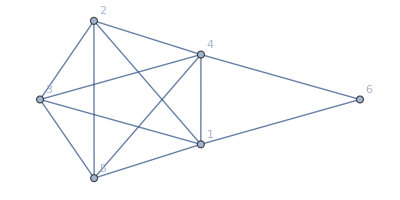

```mathematica
AdjacencyGraph[{{0,1,1,1,1,1},{1,0,1,1,1,0},{1,1,0,1,1,0},{1,1,1,0,1,1},{1,1,1,1,0,0},{1,0,0,1,0,0}}, VertexLabels->"Name"]
```

```mathematica
allGraphs6[7173698,"matrix"]//MatrixForm
```

Missing[KeyAbsent,7173698]

```mathematica
Table[With[{patt=SymbolToSets[allGraphs5[k,"colofour"]]},
{
k,
allGraphs5[k,"colofour"],
Fold[And,Map[PartitionHasPattern[SymbolToSets[#],patt]&,ListofVars[allGraphs6[GraphMatrixSignature[EmbedGraph5In6Matrix[k,7171430]],"colofour"]]]]}],{k,allGraphs5AtomKeys}]
```

SymbolName::sym: Argument Missing[KeyAbsent,7173698] at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1],x].

FromDigits::nlst: The expression StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1] is not a list of digits or a string of valid digits.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Characters[FromDigits[StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1]]],{33}].

Intersection::heads: Heads List and Characters at positions 2 and 1 are expected to be the same.

SymbolName::sym: Argument Missing[KeyAbsent,7173710] at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,7173710]],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Missing[KeyAbsent,7173710]],1],x].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringDrop[SymbolName[Missing[KeyAbsent,7173710]],1] is not a list of digits or a string of valid digits.

Intersection::heads: Heads List and Characters at positions 2 and 1 are expected to be the same.

SymbolName::sym: Argument Missing[KeyAbsent,7173833] at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,7173833]],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringDrop[SymbolName[Missing[KeyAbsent,7173833]],1] is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

Intersection::heads: Heads List and Characters at positions 2 and 1 are expected to be the same.

General::stop: Further output of Intersection::heads will be suppressed during this calculation.

{{29524,v1x2x3x4x5,False},{29525,v1x2x3x45,False},{29527,v1x2x35x4,False},{29533,v1x2x34x5,False},{29537,v1x2x345,False},{29551,v1x25x3x4,False},{29560,v1x25x34,True},{29605,v1x24x3x5,False},{29608,v1x24x35,True},{29633,v1x245x3,False},{29767,v1x23x4x5,False},{29768,v1x23x45,False},{29797,v1x235x4,True},{29857,v1x234x5,True},{29888,v1x2345,True},{30253,v15x2x3x4,False},{30262,v15x2x34,False},{30334,v15x24x3,False},{30496,v15x23x4,False},{30586,v15x234,True},{31711,v14x2x3x5,False},{31714,v14x2x35,False},{31738,v14x25x3,False},{31954,v14x23x5,False},{31984,v14x235,True},{32441,v145x2x3,False},{32684,v145x23,False},{36085,v13x2x4x5,False},{36086,v13x2x45,False},{36112,v13x25x4,True},{36166,v13x24x5,True},{36194,v13x245,True},{36817,v135x2x4,False},{36898,v135x24,True},{38281,v134x2x5,False},{38308,v134x25,True},{39014,v1345x2,False},{49207,v12x3x4x5,False},{49208,v12x3x45,False},{49210,v12x35x4,True},{49216,v12x34x5,True},{49220,v12x345,True},{49963,v125x3x4,False},{49972,v125x34,True},{51475,v124x3x5,False},{51478,v124x35,True},{52232,v1245x3,False},{56011,v123x4x5,True},{56012,v123x45,True},{56770,v1235x4,True},{58288,v1234x5,True},{59048,v12345,True}}

```mathematica
CheckHypo[key6_]:=Fold[And,
Table[With[{patt=SymbolToSets[allGraphs5[k,"colofour"]]},
Fold[And,Map[PartitionHasPattern[SymbolToSets[#],patt]&,ListofVars[allGraphs6[GraphMatrixSignature[EmbedGraph5In6Matrix[k,key6]],"colofour"]]]]],{k,allGraphs5AtomKeys}]
]
```

```mathematica
CheckHypo[7171430]
```

SymbolName::sym: Argument Missing[KeyAbsent,7173698] at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1],x].

FromDigits::nlst: The expression StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1] is not a list of digits or a string of valid digits.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Characters[FromDigits[StringDrop[SymbolName[Missing[KeyAbsent,7173698]],1]]],{33}].

Intersection::heads: Heads List and Characters at positions 2 and 1 are expected to be the same.

SymbolName::sym: Argument Missing[KeyAbsent,7173710] at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,7173710]],1].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[StringDrop[SymbolName[Missing[KeyAbsent,7173710]],1],x].

General::stop: Further output of StringSplit::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringDrop[SymbolName[Missing[KeyAbsent,7173710]],1] is not a list of digits or a string of valid digits.

Intersection::heads: Heads List and Characters at positions 2 and 1 are expected to be the same.

SymbolName::sym: Argument Missing[KeyAbsent,7173833] at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[Missing[KeyAbsent,7173833]],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringDrop[SymbolName[Missing[KeyAbsent,7173833]],1] is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

Intersection::heads: Heads List and Characters at positions 2 and 1 are expected to be the same.

General::stop: Further output of Intersection::heads will be suppressed during this calculation.

False